# All-in-one Calculation of P(ONI)

## 1. Calculation of P(CP | R’=m) 1.1With assumption (not used in the final paper)

```mathematica
ClearAll[μ,λ,p0,p1,m,n,nDef,i,j,cpWithmrprime,cpWithmrprimeMatrix];
(* probability that no r' in a single process *)
p0 = 1/2 (1+(λ /(μ+λ))^2);
(* probability that there is exactly one r' in a single process *)
p1=((2λ+μ)^2)/(2(μ+λ)^2)(1/2)(μ/(μ+λ));
(* probability that there are m r's in n-1 processes; with the assumption that there is at most one r' in a single process *)
cpWithmrprime[n_Integer,m_Integer]:=Binomial[n-1,m](p1^m) p0^(n-1-m);
(* a matrix of numerical results *)
nDef = 15;
(cpWithmrprimeMatrix = Map[(cpWithmrprime[#[[1]],#[[2]]]/.{λ->10,μ->10})&,Table[{n,m},{n,2,nDef,2},{m,0,nDef}],
{2}
])//N //MatrixForm;
```

### 1.2 Without assumption

```mathematica
ClearAll[λ,μ,nDef,nMin,mDef,p0,r,s,cp,cpPlot,cpConditionalPlot,cpYesNoProb,cpYesNoProbPlot]
```

```mathematica
r = (2 λ + μ)^2/(2(μ + λ)^2);s = (1/2) (μ)/(μ + λ);p0= (1/2) (1 + ((λ)/(μ + λ))^2);
```

```mathematica
(* nDef: default value for "Client processes" (not for "replicas"); mDef: default values for m *)
```

```mathematica
nDef = 15;mDef = 15;nMin = 2;
```

```mathematica
λ = 10;μ = 10;
```

```mathematica
(* Numerical results on Concurrency Pattern conditioning on m *)
```

```mathematica
cp = Map[If[#[[2]]>0,
Sum[Binomial[#[[1]]-1,k] Binomial[#[[2]]-1,#[[1]]-k-2](p0^k)(r^(#[[1]]-k-1))(s^#[[2]]),{k,0,#[[1]]-2}],p0^(#[[1]]-1)]&,
Table[{n,m},{n,nMin,nDef,1},{m,0,mDef}],
{2}
]//N;
```

```mathematica
(* Probability of "concurrency patterns show up or not" *)
cpYesNoProb = Map[{{#,(1- p0^(#-1))}, {#,p0^(#-1)}}&,Table[n,{n,nMin,nDef,1}]]//N;
```

```mathematica
(* Plot for Concurrency Patterns conditioning on m *)
```

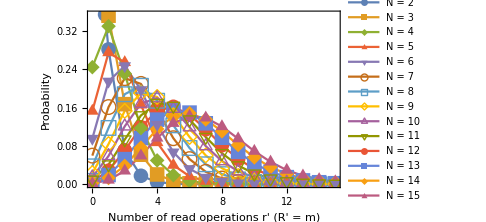

```mathematica
cpConditionalPlot = ListPlot[cp,
Joined->True,ImageSize->Medium,Frame->True,
PlotMarkers->{Automatic,15},
FrameTicks-> {Range[0,mDef], Automatic},
DataRange->{0,mDef},
PlotRange->Automatic,
AspectRatio->1/GoldenRatio,
LabelStyle->{GrayLevel[0]},FrameLabel->{{"Probability",None},{"Number of read operations r' (R' = m)",Row[{"b) Conditional probability of concurrency patterns"}]}},
FrameStyle->Directive[FontSize->14,FontFamily->"Helvetica"],
PlotRange->All,Axes->True,
PlotLegends->{Map["N = "<>#&,IntegerString[Table[i,{i,nMin,nDef,1}]]]}]
```

```mathematica
Export["D:\\GitHub\\Paper_VLDB15_2AM\\src\\resource\\"<>"vldb-concurrency-pattern-numerical-results.pdf",cpConditionalPlot];
Export["D:\\GitHub\\Paper_VLDB15_2AM\\src\\fig\\"<>"vldb-concurrency-pattern-numerical-results.pdf",cpConditionalPlot];
```

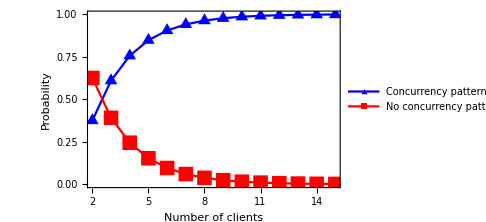

```mathematica
cpYesNoProbPlot = ListPlot[Transpose[cpYesNoProb],
Joined->True,ImageSize->Medium,Frame->True,
PlotMarkers->{{▲,15},{■,15}},
FrameTicks-> {Range[nMin,nDef,1], Automatic},
AspectRatio->1/GoldenRatio,
LabelStyle->{GrayLevel[0]},FrameLabel->{{"Probability",None},{"Number of clients",Row[{"a) Probability of concurrency patterns"}]}},
FrameStyle->Directive[FontSize->14,FontFamily->"Helvetica"],
PlotRange->All,
DataRange->{nMin,nDef},
Axes->True,AxesLabel->Automatic,
PlotStyle->{Blue,Red},
PlotLegends->{"Concurrency patterns","No concurrency patterns"}]
```

```mathematica
Export["D:\\GitHub\\Paper_VLDB15_2AM\\src\\resource\\"<>"vldb-concurrency-pattern-yes-no.pdf",cpYesNoProbPlot];
Export["D:\\GitHub\\Paper_VLDB15_2AM\\src\\fig\\"<>"vldb-concurrency-pattern-yes-no.pdf",cpYesNoProbPlot];
```

```mathematica
cpPlot = Grid[{{cpYesNoProbPlot,cpConditionalPlot}}]
```

-Graphics- | -Graphics-

```mathematica
Export["D:\\GitHub\\Paper_VLDB15_2AM\\src\\resource\\"<>"vldb-concurrency-pattern-plot.pdf",cpPlot];
Export["D:\\GitHub\\Paper_VLDB15_2AM\\src\\fig\\"<>"vldb-concurrency-pattern-plot.pdf",cpPlot];
```

## 2. Calculation of P(RWP | R’=m)

### 2.1 Calculation of P(r != R(w))

```mathematica
(* Calcuation of the first part of rwp (read-write pattern); *)
```

```mathematica
ClearAll[replicaNum,replicaAxis,t1,q,α,μr,μw,rwp1Prob,rwp1ProbTable];
```

```mathematica
replicaNum = 15; (* max number of replicas *)
```

```mathematica
replicaAxis = Table[i,{i,nMin,replicaNum}];
```

```mathematica
t1=0.1;(* expected time lag *)
μr=20;μw=20; (* expected message delay for read (ur) and write (uw) operations *)
```

```mathematica
(* formula for P(r≠R(w)) 
n: local parameter for the number of replicas; q is a majority;
*)
```

```mathematica
rwp1Prob[n_Integer]:=Module[{q = Floor[n/2]+1, α = (μr)/(μr + μw)},
Exp[-q  μw t1](α^q Beta[q,α(n-q)+1])/(Beta[q,n-q+1])
]
```

```mathematica
(* a table of numerical results *)
```

```mathematica
rwp1ProbTable = rwp1Prob[#]&/@replicaAxis
```

{0.00457891,0.00732626,0.000566572,0.00077461,0.0000628992,0.0000813243,6.77295×10^-6,8.51249×10^-6,7.20025×10^-7,8.8966×10^-7,7.60436×10^-8,9.28973×10^-8,8.00055×10^-9,9.69478×10^-9}

### 2.2 Calculation of P(r’ != R(w))

```mathematica
(*
(*  
s is an integral variable; 
t1 and t2 are the expected time lags for part1 and part2, respectively;ur (for read) and uw (for write) are expections of the random variables for message delay;
rwp2Prob is the formula about the probability of the second part of read-write pattern;
rwp2ProbTable is a table of the numerical results for the second part of read-write pattern;
*)
ClearAll[n,q,s,t2,μr,μw,rwp2Prob,rwp2ProbTable];

(* t is the expected time lag *)
t2=0.05;μr=20;μw=20;
(* formula for P(r'≠R(w)) *)
(* n: local parameter for the number of replicas; q is a majority; *)
rwp2Prob[n_Integer] := Module[{q = Floor[n/2]+1},
q Binomial[n,q](
μr Integrate[Exp[-μr s (n-q+1)](1-Exp[-μr s])^(q-1),{s,0,t2}]+
(μr^q Exp[μw t2] Integrate[Exp[-(μr+μw) s]((1-Exp[-μr t2])/(μr)+Exp[μw t2] ((Exp[-(μr+μw) t2]-Exp[-(μr+μw) s])/(μr+μw)))^(q-1)Exp[-μr(n-q)s],
{s,t2,Infinity}]
))
]
(* a table of numerical results *)
rwp2ProbTable = rwp2Prob[#]&/@replicaAxis 
*)
```

### 2.3 Calculation of P(r’ != R(w) | r != R(w))

#### 2.3.1 Using the derived formula

```mathematica
ClearAll[rwp2Formula,q,n,λr,λw,t2,rwp2ProbTable];
t2=0.05;λr=20;λw=20;
rwp2Formula[n_Integer?Positive] := Module[{q=Floor[n/2]+1,s,k},(λr Integrate[Exp[-λr(n-q+1)s](1-Exp[-λr s])^(q-1),{s,0,t2}]
+Sum[((Binomial[q-1,k-1]Binomial[n-q,n-q-k])/Binomial[n,n-q])λr^q Exp[λw t2]Integrate[Exp[-(λr + λw)s]((1-Exp[-λr t2])/(λr)+Exp[λw t2] ((Exp[-(λr+λw) t2]-Exp[-(λr+λw) s])/(λr+λw)))^(k-1)
((1-Exp[-λr s])/λr)^(q-k)Exp[-λr(n-q)s],{s,t2,Infinity}],
{k,0,n-q}]
+Sum[((Binomial[q-1,k]Binomial[n-q,n-q-k])/Binomial[n,n-q])
λr^q
Integrate[Exp[-λr s]((1-Exp[-λr t2])/(λr)+Exp[λw t2] ((Exp[-(λr+λw) t2]-Exp[-(λr+λw) s])/(λr+λw)))^(k)
((1-Exp[-λr s])/λr)^(q-1-k)Exp[-λr(n-q)s],{s,t2,Infinity}],
{k,0,n-q}])/Beta[q,n-q+1]
]
rwp2Formula2 = rwp2Formula[2];
rwp2ProbTable=Prepend[Table[rwp2Formula[i],{i,3,replicaNum}],0.0]
```

{0.,0.959037,0.943863,0.964337,0.94886,0.970553,0.957339,0.975624,0.964676,0.979635,0.970581,0.982829,0.975303,0.985405}

#### 2.3.2 Using the original formula

```mathematica
(*
Clear[f,t2,n,q,xbounds, bounds,x,s,t2,λr,λw];
n=10;λr=20;λw=20;t2=0.05;
q=Floor[n/2]+1;
(* integral bounds over each x_i *)xbounds = Table[{Subscript[x,i],0,s},{i,q,2,-1}];(* adding the leftmost integral bound over s *) bounds=Prepend[xbounds,{s,0,Infinity}];
(* integrand function *)
rwp2OriginalFormula=
Sum[(Binomial[q-1,k-1]Binomial[n-q,n-q-k]/Binomial[n,n-q])
Integrate[(Exp[λw(t2-s)])^(Boole[s>t2])
(Product[(Exp[λw(t2-Subscript[x,i])])^(Boole[Subscript[x,i]>t2]),{i,2,k}])
Exp[-λr(n-q)s]
λr Exp[-λr s]Product[λr Exp[-λr Subscript[x,i]],{i,2,q}],
Sequence@@bounds]
+(Binomial[q-1,k]Binomial[n-q,n-q-k]/Binomial[n,n-q])
Integrate[(Product[(Exp[λw(t2-Subscript[x,i])])^(Boole[Subscript[x,i]>t2]),{i,2,k+1}])
Exp[-λr(n-q)s]
λr Exp[-λr s]Product[λr Exp[-λr Subscript[x,i]],{i,2,q}],
Sequence@@bounds],
{k,0,n-q}]/Beta[q,n-q+1]
*)
```

### 2.4 Plotting of P(r != R(w)) and 1 - P(r’ != R(w) | r != R(w))

```mathematica
ClearAll[rwpPlot];
(* use ListLogPlot to gracefully show small numbers and large numbers together *)
rwpPlot =ListLogPlot[{Transpose[{replicaAxis,rwp1ProbTable}],Transpose[{replicaAxis,(*MapThread[(1-#1^(#2-1))&,{rwp2ProbTable,replicaAxis}]*)1-rwp2ProbTable}]},
Joined->True,ImageSize->600,Frame->True,
FrameStyle->Directive[FontSize->14,FontFamily->"Helvetica"],
FrameTicks-> {Range[1,replicaNum,2], Automatic},
AspectRatio->1/GoldenRatio,
LabelStyle->{GrayLevel[0]},
FrameLabel->{{"Probability",None},{"Number of replicas",None(*Row[{"Probability of read-write patterns"}]*)}},
PlotMarkers->{{▲,15},{■,15}},
DataRange->{nMin,replicaNum,1},
PlotRange->Automatic,
Axes->True,AxesLabel->Automatic,
PlotStyle->{Red,Blue},
PlotLegends->Placed[LineLegend[{"P{r ≠ R(w)}","1-P{r' ≠ R(w)|r ≠ R(w)}"}],{After,Right}]
]
(* Notice: For P{r ≠ R(w)}, the data for odd or even number of replicas fit well with exponential functions Exp(a x + b),respectively *)
(* exported as pdf *)
Export["D:\\GitHub\\Paper_VLDB15_2AM\\src\\resource\\"<>"vldb-rwp-pattern-plot-2.pdf",rwpPlot];
Export["D:\\GitHub\\Paper_VLDB15_2AM\\src\\fig\\"<>"vldb-rwp-pattern-plot-2.pdf",rwpPlot];
```

-Graphics-

### 2.5 Calcuation of P(RWP | R’=m)

```mathematica
ClearAll[rwpMTable,rwp2ReverseProbTable]
```

```mathematica
(* rwp2ReverseProbTable = 1 - rwp2ProbTable^m *)
```

```mathematica
rwp2ReverseProbTable[m_Integer]:=1-rwp2ProbTable^m
```

```mathematica
(* rwpM = rwp1 * rwp2Reverse *)
```

```mathematica
rwpMTable[m_Integer] := MapThread[(#1 #2)&,{rwp1ProbTable,1-rwp2ProbTable^m}]
```

## 3. Calculation of P(ONI)

### 3.1 Formulas and numerical evaluations

```mathematica
ClearAll[rwpMNProb,cpMNProb,α,r,s,μ,λ,μr,μw,rwpProbMatrix,cpProbMatrix,oniProbMatrix,t1,t2,rwpProbTable,cpProbTable,oniProbTable,oniProbPlot];
```

```mathematica
μ=10;λ=10;
r = (2 λ + μ)^2/(2(μ + λ)^2);s = (1/2) (μ)/(μ + λ);p0= (1/2) (1 + ((λ)/(μ + λ))^2);
μr=20;μw=20;
t1=0.1;t2=0.05;
```

```mathematica
(* n: number of replicas; N: number of clients; m: number of r' *)
```

```mathematica
(* calcuation of the probability of read-write patterns, with parameters m and n *)
```

```mathematica
rwpMNProb[n_Integer,N_Integer,m_Integer]:=
Module[{q=Floor[n/2]+1,α = (μr)/(μr + μw),s,k},
Exp[-q  μw t1](α^q Beta[q,α(n-q)+1])/(Beta[q,n-q+1])
(1-
(
(λr Integrate[Exp[-λr(n-q+1)s](1-Exp[-λr s])^(q-1),{s,0,t2}]
+Sum[((Binomial[q-1,k-1]Binomial[n-q,n-q-k])/Binomial[n,n-q])λr^q Exp[λw t2]Integrate[Exp[-(λr + λw)s]((1-Exp[-λr t2])/(λr)+Exp[λw t2] ((Exp[-(λr+λw) t2]-Exp[-(λr+λw) s])/(λr+λw)))^(k-1)
((1-Exp[-λr s])/λr)^(q-k)Exp[-λr(n-q)s],{s,t2,Infinity}],
{k,0,n-q}]
+Sum[((Binomial[q-1,k]Binomial[n-q,n-q-k])/Binomial[n,n-q])
λr^q
Integrate[Exp[-λr s]((1-Exp[-λr t2])/(λr)+Exp[λw t2] ((Exp[-(λr+λw) t2]-Exp[-(λr+λw) s])/(λr+λw)))^(k)
((1-Exp[-λr s])/λr)^(q-1-k)Exp[-λr(n-q)s],{s,t2,Infinity}],
{k,0,n-q}])/Beta[q,n-q+1]
)^m
)
];
(* calculation of the probability of concurrency patterns, with paramaters m and N *)
cpMNProb[N_Integer,m_Integer] :=Sum[Binomial[N-1,k] Binomial[m-1,N-k-2](p0^k)(r^(N-k-1))(s^m),{k,0,N-2}];
```

```mathematica
(* calculation of the probability of old-new inversions, with parameters n,N, and m *)
```

```mathematica
oniMNProb[n_Integer,N_Integer,m_Integer]:=rwpMNProb[n,m]cpMNProb[N,m];
(* matrices of numerical results about the probability of read-write patterns, concurrency patterns, and old-new inversinos, respectively *)
cpMatrix=ParallelTable[cpMNProb[j,k],{j,1,100,1},{k,1,j-1}]//N;
rwpMatrix = ParallelTable[rwpMNProb[3,j,k],{j,20,100,20},{k,1,j-1}]//N;
```

LinkObject::linkd: Unable to communicate with closed link LinkObject["/usr/local/Wolfram/Mathematica/10.3/Executables/wolfram" -subkernel -noinit -wstp,364,6].

Kernels::rdead: Subkernel connected through KernelObject[2,local] appears dead.

Parallel`Developer`QueueRun::req: Requeueing evaluations {15} assigned to KernelObject[2,local,<defunct>].

LaunchKernels::clone: Kernel KernelObject[2,local,<defunct>] resurrected as KernelObject[5,local].

LinkObject::linkd: Unable to communicate with closed link LinkObject["/usr/local/Wolfram/Mathematica/10.3/Executables/wolfram" -subkernel -noinit -wstp,366,8].

Kernels::rdead: Subkernel connected through KernelObject[4,local] appears dead.

Parallel`Developer`QueueRun::req: Requeueing evaluations {13} assigned to KernelObject[4,local,<defunct>].

LaunchKernels::clone: Kernel KernelObject[4,local,<defunct>] resurrected as KernelObject[6,local].

LinkObject::linkd: Unable to communicate with closed link LinkObject["/usr/local/Wolfram/Mathematica/10.3/Executables/wolfram" -subkernel -noinit -wstp,363,5].

General::stop: Further output of LinkObject::linkd will be suppressed during this calculation.

Kernels::rdead: Subkernel connected through KernelObject[1,local] appears dead.

General::stop: Further output of Kernels::rdead will be suppressed during this calculation.

Parallel`Developer`QueueRun::req: Requeueing evaluations {16} assigned to KernelObject[1,local,<defunct>].

General::stop: Further output of Parallel`Developer`QueueRun::req will be suppressed during this calculation.

LaunchKernels::clone: Kernel KernelObject[1,local,<defunct>] resurrected as KernelObject[7,local].

General::stop: Further output of LaunchKernels::clone will be suppressed during this calculation.

```mathematica
{rwpProbMatrix,cpProbMatrix,oniProbMatrix}=Apply[#,Table[{i,j},{i,nMin,replicaNum,1},{j,1,i-1}],{2}]&/@{rwpMNProb,cpMNProb,oniMNProb};
```

```mathematica
(*(rwpProbMatrix=Map[rwpMNProb[#[[1]],#[[2]]]&,Table[{i,j},{i,2,replicaNum,1},{j,1,i-1}],{2}])//MatrixForm
(cpProbMatrix=Map[cpMNProb[#[[1]],#[[2]]]&,Table[{i,j},{i,2,replicaNum,1},{j,1,i-1}],{2}])//MatrixForm
(oniProbMatrix=Map[oniMNProb[#[[1]],#[[2]]]&,Table[{i,j},{i,2,replicaNum,1},{j,1,i-1}],{2}])//MatrixForm*)
```

```mathematica
cpMatrix//MatrixForm
```

```mathematica
rwpMatrix//MatrixForm
```

rwpMatrix

```mathematica
(* summing over m to get tables of the probabilities of read-write patterns, concurrency patterns, and old-new inversions, respectively *)
{rwpProbTable,cpProbTable,oniProbTable}=Map[Total[#,{2}]&,{rwpProbMatrix,cpProbMatrix,oniProbMatrix}];
```

### 3.2 Plotting

```mathematica
oniProbPlot =ListLogPlot[Map[Transpose[{replicaAxis,#}]&,{cpProbTable,rwpProbTable,oniProbTable}],
Joined->True,ImageSize->550,Frame->True,
FrameStyle->Directive[FontSize->14,FontFamily->"Helvetica"],
FrameTicks-> {Range[1,replicaNum,2], Automatic},
AspectRatio->1/GoldenRatio,
LabelStyle->{GrayLevel[0]},
FrameLabel->{{"Probability",None},{"Number of replicas",None(*Row[{"Probability of read-write patterns"}]*)}},
PlotMarkers->{{▲,15},{■,15},{◆,15}},
DataRange->{nMin,replicaNum,1},
PlotRange->Automatic,
Axes->True,AxesLabel->Automatic,
PlotStyle->{Red,Blue,Brown},
PlotLegends->Placed[LineLegend[{"Concurrency pattern","Read-write pattern","Old-new inversion"}],{After,Right}]
]
```

-Graphics-

```mathematica
(* exported as pdf *)
```

```mathematica
Export["D:\\GitHub\\Paper_VLDB15_2AM\\src\\resource\\"<>"vldb-cp-rwp-oni-plot.pdf",oniProbPlot];
Export["D:\\GitHub\\Paper_VLDB15_2AM\\src\\fig\\"<>"vldb-cp-rwp-oni-plot.pdf",oniProbPlot];
```

### 3.3 Making tables

```mathematica
(* table for P(CP), P(RWP|CP), and P(ONI) *)
```

```mathematica
Grid[Prepend[Transpose[{replicaAxis,cpProbTable,rwpProbTable,oniProbTable}],{"# replicas","P(CP)","P(RWP|CP)","P(ONI)"}],Alignment->Left,Spacings->{2,1},Frame->All]//N
```

# replicas | P(CP) | P(RWP|CP) | P(ONI)
2. | 0.28125 | -1.01672×10^-18 | -2.85953×10^-19
3. | 0.518555 | 0.00088802 | 0.000203683
4. | 0.677307 | 0.000183791 | 0.0000352958
5. | 0.781222 | 0.000266569 | 0.0000437181
6. | 0.849318 | 0.0000450835 | 6.49226×10^-6
7. | 0.89429 | 0.0000478926 | 6.08721×10^-6
8. | 0.924335 | 7.43561×10^-6 | 8.5381×10^-7
9. | 0.9447 | 7.06025×10^-6 | 7.30744×10^-7
10. | 0.95874 | 1.04312×10^-6 | 9.93356×10^-8
11. | 0.968604 | 9.37995×10^-7 | 8.16935×10^-8
12. | 0.975675 | 1.34085×10^-7 | 1.08822×10^-8
13. | 0.98085 | 1.16911×10^-7 | 8.77158×10^-9
14. | 0.984717 | 1.63195×10^-8 | 1.15178×10^-9
15. | 0.987662 | 1.39573×10^-8 | 9.18283×10^-10

```mathematica
(* table for read-write pattern part 1 "P(r \neq R(w))" and read-write pattern part 2 "1 - P(r' \neq R(w) | r \neq R(w))" *)
```

```mathematica
Grid[Prepend[Transpose[{replicaAxis,rwp1ProbTable,1-rwp2ProbTable}],{"# replicas","P(r \neq R(w))","1 - P(r' \neq R(w) | r \neq R(w))"}],Alignment->Left,Spacings->{2,1},Frame->All]
```

# replicas | P(r 
eq R(w)) | 1 - P(r' 
eq R(w) | r 
eq R(w))
2 | 0.00457891 | 1.
3 | 0.00732626 | 0.0409628
4 | 0.000566572 | 0.0561367
5 | 0.00077461 | 0.0356626
6 | 0.0000628992 | 0.0511399
7 | 0.0000813243 | 0.0294467
8 | 6.77295×10^-6 | 0.0426608
9 | 8.51249×10^-6 | 0.0243758
10 | 7.20025×10^-7 | 0.0353241
11 | 8.8966×10^-7 | 0.0203645
12 | 7.60436×10^-8 | 0.0294186
13 | 9.28973×10^-8 | 0.0171705
14 | 8.00055×10^-9 | 0.0246974
15 | 9.69478×10^-9 | 0.0145951

### 3.4 Interactive manipulation

## Section 4 Tests

```mathematica
cpYesNoProb//MatrixForm
```

((2.
0.375) | (2.
0.625)
(3.
0.609375) | (3.
0.390625)
(4.
0.755859) | (4.
0.244141)
(5.
0.847412) | (5.
0.152588)
(6.
0.904633) | (6.
0.0953674)
(7.
0.940395) | (7.
0.0596046)
(8.
0.962747) | (8.
0.0372529)
(9.
0.976717) | (9.
0.0232831)
(10.
0.985448) | (10.
0.0145519)
(11.
0.990905) | (11.
0.00909495)
(12.
0.994316) | (12.
0.00568434)
(13.
0.996447) | (13.
0.00355271)
(14.
0.99778) | (14.
0.00222045)
(15.
0.998612) | (15.
0.00138778))

```mathematica
Flatten[%144]
```

{2.,0.375,2.,0.625,3.,0.609375,3.,0.390625,4.,0.755859,4.,0.244141,5.,0.847412,5.,0.152588,6.,0.904633,6.,0.0953674,7.,0.940395,7.,0.0596046,8.,0.962747,8.,0.0372529,9.,0.976717,9.,0.0232831,10.,0.985448,10.,0.0145519,11.,0.990905,11.,0.00909495,12.,0.994316,12.,0.00568434,13.,0.996447,13.,0.00355271,14.,0.99778,14.,0.00222045,15.,0.998612,15.,0.00138778}

```mathematica
cp//MatrixForm
```

(0.625 | 0.28125 | 0.0703125 | 0.0175781 | 0.00439453 | 0.00109863 | 0.000274658 | 0.0000686646 | 0.0000171661 | 4.29153×10^-6 | 1.07288×10^-6 | 2.68221×10^-7 | 6.70552×10^-8 | 1.67638×10^-8 | 4.19095×10^-9 | 1.04774×10^-9
0.390625 | 0.351563 | 0.166992 | 0.0615234 | 0.0203247 | 0.00631714 | 0.00188828 | 0.000549316 | 0.000156641 | 0.0000439882 | 0.0000122041 | 3.35276×10^-6 | 9.13627×10^-7 | 2.47266×10^-7 | 6.65314×10^-8 | 1.78115×10^-8
0.244141 | 0.32959 | 0.230713 | 0.117004 | 0.0496445 | 0.0188999 | 0.00669479 | 0.00225306 | 0.000729829 | 0.00022953 | 0.0000705086 | 0.0000212481 | 6.30214×10^-6 | 1.84428×10^-6 | 5.33561×10^-7 | 1.52839×10^-7
0.152588 | 0.274658 | 0.254059 | 0.165482 | 0.0870237 | 0.0397739 | 0.0164902 | 0.00636756 | 0.00232967 | 0.000817101 | 0.000277034 | 0.0000913523 | 0.0000294329 | 9.29867×10^-6 | 2.88868×10^-6 | 8.84389×10^-7
0.0953674 | 0.214577 | 0.246763 | 0.196874 | 0.124294 | 0.0668101 | 0.0319806 | 0.0140362 | 0.00576103 | 0.00224215 | 0.000835823 | 0.00030068 | 0.000104985 | 0.0000357369 | 0.000011902 | 3.88933×10^-6
0.0596046 | 0.160933 | 0.221282 | 0.209212 | 0.154596 | 0.0959419 | 0.0523247 | 0.0258513 | 0.011818 | 0.00507598 | 0.00207165 | 0.000810316 | 0.000305779 | 0.000111904 | 0.0000398817 | 0.000013889
0.0372529 | 0.117347 | 0.187755 | 0.205357 | 0.174113 | 0.122816 | 0.0753998 | 0.0415476 | 0.0210046 | 0.00990088 | 0.0044045 | 0.00186653 | 0.000759034 | 0.000297921 | 0.000113394 | 0.0000420144
0.0232831 | 0.083819 | 0.15297 | 0.19006 | 0.182005 | 0.144026 | 0.0984833 | 0.0600131 | 0.0333246 | 0.0171448 | 0.00827661 | 0.0037863 | 0.00165429 | 0.000694651 | 0.000281774 | 0.000110877
0.0145519 | 0.0589353 | 0.120817 | 0.168113 | 0.179539 | 0.157651 | 0.118968 | 0.0795606 | 0.0482196 | 0.026936 | 0.01405 | 0.0069135 | 0.00323559 | 0.00144984 | 0.0006254 | 0.00026087
0.00909495 | 0.0409273 | 0.0931095 | 0.14345 | 0.169088 | 0.163247 | 0.134873 | 0.0983147 | 0.064661 | 0.0390277 | 0.0219051 | 0.0115535 | 0.0057748 | 0.0027543 | 0.00126068 | 0.000556389
0.00568434 | 0.0281375 | 0.0703437 | 0.118881 | 0.153332 | 0.161498 | 0.145076 | 0.114575 | 0.0813462 | 0.0528115 | 0.0317721 | 0.0179021 | 0.00952895 | 0.00482553 | 0.00233859 | 0.00108998
0.00355271 | 0.0191847 | 0.0522782 | 0.0961631 | 0.134733 | 0.153786 | 0.149306 | 0.12707 | 0.0969308 | 0.0674082 | 0.043311 | 0.0259881 | 0.0146904 | 0.00787967 | 0.00403473 | 0.00198224
0.00222045 | 0.0129896 | 0.0383193 | 0.0762165 | 0.115283 | 0.141779 | 0.147984 | 0.135078 | 0.110235 | 0.0818052 | 0.0559467 | 0.0356431 | 0.0213408 | 0.0120963 | 0.00653073 | 0.00337593
0.00138778 | 0.00874301 | 0.027759 | 0.059365 | 0.0964201 | 0.127127 | 0.141994 | 0.138421 | 0.120387 | 0.0950044 | 0.0689435 | 0.0465061 | 0.0294199 | 0.0175827 | 0.00998943 | 0.00542365)

```mathematica
Transpose[cp]//MatrixForm
```

(0.625 | 0.390625 | 0.244141 | 0.152588 | 0.0953674 | 0.0596046 | 0.0372529 | 0.0232831 | 0.0145519 | 0.00909495 | 0.00568434 | 0.00355271 | 0.00222045 | 0.00138778
0.28125 | 0.351563 | 0.32959 | 0.274658 | 0.214577 | 0.160933 | 0.117347 | 0.083819 | 0.0589353 | 0.0409273 | 0.0281375 | 0.0191847 | 0.0129896 | 0.00874301
0.0703125 | 0.166992 | 0.230713 | 0.254059 | 0.246763 | 0.221282 | 0.187755 | 0.15297 | 0.120817 | 0.0931095 | 0.0703437 | 0.0522782 | 0.0383193 | 0.027759
0.0175781 | 0.0615234 | 0.117004 | 0.165482 | 0.196874 | 0.209212 | 0.205357 | 0.19006 | 0.168113 | 0.14345 | 0.118881 | 0.0961631 | 0.0762165 | 0.059365
0.00439453 | 0.0203247 | 0.0496445 | 0.0870237 | 0.124294 | 0.154596 | 0.174113 | 0.182005 | 0.179539 | 0.169088 | 0.153332 | 0.134733 | 0.115283 | 0.0964201
0.00109863 | 0.00631714 | 0.0188999 | 0.0397739 | 0.0668101 | 0.0959419 | 0.122816 | 0.144026 | 0.157651 | 0.163247 | 0.161498 | 0.153786 | 0.141779 | 0.127127
0.000274658 | 0.00188828 | 0.00669479 | 0.0164902 | 0.0319806 | 0.0523247 | 0.0753998 | 0.0984833 | 0.118968 | 0.134873 | 0.145076 | 0.149306 | 0.147984 | 0.141994
0.0000686646 | 0.000549316 | 0.00225306 | 0.00636756 | 0.0140362 | 0.0258513 | 0.0415476 | 0.0600131 | 0.0795606 | 0.0983147 | 0.114575 | 0.12707 | 0.135078 | 0.138421
0.0000171661 | 0.000156641 | 0.000729829 | 0.00232967 | 0.00576103 | 0.011818 | 0.0210046 | 0.0333246 | 0.0482196 | 0.064661 | 0.0813462 | 0.0969308 | 0.110235 | 0.120387
4.29153×10^-6 | 0.0000439882 | 0.00022953 | 0.000817101 | 0.00224215 | 0.00507598 | 0.00990088 | 0.0171448 | 0.026936 | 0.0390277 | 0.0528115 | 0.0674082 | 0.0818052 | 0.0950044
1.07288×10^-6 | 0.0000122041 | 0.0000705086 | 0.000277034 | 0.000835823 | 0.00207165 | 0.0044045 | 0.00827661 | 0.01405 | 0.0219051 | 0.0317721 | 0.043311 | 0.0559467 | 0.0689435
2.68221×10^-7 | 3.35276×10^-6 | 0.0000212481 | 0.0000913523 | 0.00030068 | 0.000810316 | 0.00186653 | 0.0037863 | 0.0069135 | 0.0115535 | 0.0179021 | 0.0259881 | 0.0356431 | 0.0465061
6.70552×10^-8 | 9.13627×10^-7 | 6.30214×10^-6 | 0.0000294329 | 0.000104985 | 0.000305779 | 0.000759034 | 0.00165429 | 0.00323559 | 0.0057748 | 0.00952895 | 0.0146904 | 0.0213408 | 0.0294199
1.67638×10^-8 | 2.47266×10^-7 | 1.84428×10^-6 | 9.29867×10^-6 | 0.0000357369 | 0.000111904 | 0.000297921 | 0.000694651 | 0.00144984 | 0.0027543 | 0.00482553 | 0.00787967 | 0.0120963 | 0.0175827
4.19095×10^-9 | 6.65314×10^-8 | 5.33561×10^-7 | 2.88868×10^-6 | 0.000011902 | 0.0000398817 | 0.000113394 | 0.000281774 | 0.0006254 | 0.00126068 | 0.00233859 | 0.00403473 | 0.00653073 | 0.00998943
1.04774×10^-9 | 1.78115×10^-8 | 1.52839×10^-7 | 8.84389×10^-7 | 3.88933×10^-6 | 0.000013889 | 0.0000420144 | 0.000110877 | 0.00026087 | 0.000556389 | 0.00108998 | 0.00198224 | 0.00337593 | 0.00542365)

```mathematica
CP={{1},{2,3},{4,5,6}};
```

```mathematica
RWP={{10},{20,30},{40,50,60}};
```

```mathematica
CP//MatrixForm
```

({1}
{2,3}
{4,5,6})

```mathematica
RWP//MatrixForm
```

({10}
{20,30}
{40,50,60})

```mathematica
ONIm=CP RWP
```

{{10},{40,90},{160,250,360}}

```mathematica
Total[ONIm,{2}]
```

{10,130,770}